# SVM-BDS-BDT Comparison Results, 5/19/16

## Raw Data

## SVM: c, γ, Number of Support Vectors, False Positive Fraction, False Negative Fraction, Efficiency

```mathematica
SVMLinearHardRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","linearhard0519"}], "Table"];
SVMLinearSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","linearsoft0519"}], "Table"];

SVMCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","circlehard0519"}], "Table"];
SVMCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","circlesoft0519"}], "Table"];

SVMTwoCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","twocirclehard0519"}], "Table"]
SVMTwoCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","twocirclesoft0519"}], "Table"];
```

## BDS: Number of Stumps, Efficiency, False Positive Fraction, False Negative Fraction

```mathematica
BDSLinearHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","linearhard0519"}], "Table"];
BDSLinearSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","linearsoft0519"}], "Table"];

BDSCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","circlehard0519"}], "Table"];
BDSCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","circlesoft0519"}], "Table"];

BDSTwoCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","twocirclehard0519"}], "Table"];
BDSTwoCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","twocirclesoft0519"}], "Table"];
```

## BDT: Number of Trees, Efficiency, False Positive Fraction, False Negative Fraction

```mathematica
BDTLinearHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","linearhard0519"}], "Table"];
BDTLinearSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","linearsoft0519"}], "Table"];

BDTCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","circlehard0519"}], "Table"];
BDTCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","circlesoft0519"}], "Table"];

BDTTwoCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","twocirclehard0519"}], "Table"];
BDTTwoCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","twocirclesoft0519"}], "Table"];
```

## Formatted Datasets

## SVM

### c-γ-Efficiency

```mathematica
SVMLinearHardCGE = SVMLinearHardRawData[[All,{1,2, 6}]];
SVMLinearSoftCGE = SVMLinearSoftRawData[[All,{1,2, 6}]];

SVMCircleHardCGE = SVMCircleHardRawData[[All,{1,2, 6}]];
SVMCircleSoftCGE = SVMCircleSoftRawData[[All,{1,2, 6}]];

SVMTwoCircleHardCGE = SVMTwoCircleHardRawData[[All,{1,2, 6}]];
SVMTwoCircleSoftCGE = SVMTwoCircleSoftRawData[[All,{1,2, 6}]];
```

### Log(c)-γ-Efficiency

```mathematica
SVMLinearHardLogCGE = MapAt[Log10, SVMLinearHardCGE, {All, 1}];
SVMLinearSoftLogCGE = MapAt[Log10, SVMLinearSoftCGE, {All, 1}];

SVMCircleHardLogCGE = MapAt[Log10, SVMCircleHardCGE, {All, 1}];
SVMCircleSoftLogCGE = MapAt[Log10, SVMCircleSoftCGE, {All, 1}];

SVMTwoCircleHardLogCGE = MapAt[Log10, SVMTwoCircleHardCGE, {All, 1}];
SVMTwoCircleSoftLogCGE = MapAt[Log10, SVMTwoCircleSoftCGE, {All, 1}];
```

### Efficiency-1 - False Positive Fraction

```mathematica
SVMLinearHardEFP= MapAt[1-#&,SVMLinearHardRawData[[All,{6,4}]],{All,2}];
SVMLinearSoftEFP= MapAt[1-#&,SVMLinearSoftRawData[[All,{6,4}]],{All,2}];

SVMCircleHardEFP = MapAt[1-#&,SVMCircleHardRawData[[All,{6,4}]],{All,2}];
SVMCircleSoftEFP = MapAt[1-#&,SVMCircleSoftRawData[[All,{6,4}]],{All,2}];

SVMTwoCircleHardEFP = MapAt[1-#&,SVMTwoCircleHardRawData[[All,{6,4}]],{All,2}];
SVMTwoCircleSoftEFP = MapAt[1-#&,SVMTwoCircleSoftRawData[[All,{6,4}]],{All,2}];
```

### Efficiency-1 - False Negative Fraction

```mathematica
SVMLinearHardEFN= MapAt[1-#&,SVMLinearHardRawData[[All,{6,5}]],{All,2}];
SVMLinearSoftEFN= MapAt[1-#&,SVMLinearSoftRawData[[All,{6,5}]],{All,2}];

SVMCircleHardEFN = MapAt[1-#&,SVMCircleHardRawData[[All,{6,5}]],{All,2}];
SVMCircleSoftEFN = MapAt[1-#&,SVMCircleSoftRawData[[All,{6,5}]],{All,2}];

SVMTwoCircleHardEFN = MapAt[1-#&,SVMTwoCircleHardRawData[[All,{6,5}]],{All,2}];
SVMTwoCircleSoftEFN = MapAt[1-#&,SVMTwoCircleSoftRawData[[All,{6,5}]],{All,2}];
```

### False Positive Fraction-1 - False Negative Fraction

```mathematica
SVMLinearHardFPFN= MapAt[1-#&,SVMLinearHardRawData[[All,{4,5}]],{All,2}];
SVMLinearSoftFPFN= MapAt[1-#&,SVMLinearSoftRawData[[All,{4,5}]],{All,2}];

SVMCircleHardFPFN = MapAt[1-#&,SVMCircleHardRawData[[All,{4,5}]],{All,2}];
SVMCircleSoftFPFN= MapAt[1-#&,SVMCircleSoftRawData[[All,{4,5}]],{All,2}];

SVMTwoCircleHardFPFN = MapAt[1-#&,SVMTwoCircleHardRawData[[All,{4,5}]],{All,2}];
SVMTwoCircleSoftFPFN= MapAt[1-#&,SVMTwoCircleSoftRawData[[All,{4,5}]],{All,2}];
```

## BDS

### Number of Stumps-Efficiency

```mathematica
BDSLinearHardSE = BDSLinearHardRawData[[All,{1,2}]];
BDSLinearSoftSE = BDSLinearSoftRawData[[All,{1,2}]];

BDSCircleHardSE = BDSCircleHardRawData[[All,{1,2}]];
BDSCircleSoftSE = BDSCircleSoftRawData[[All,{1,2}]];

BDSTwoCircleHardSE = BDSTwoCircleHardRawData[[All,{1,2}]];
BDSTwoCircleSoftSE = BDSTwoCircleSoftRawData[[All,{1,2}]];
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDSLinearHardEFP = MapAt[1-#&,BDSLinearHardRawData[[All,{2,3}]],{All,2}];
BDSLinearSoftEFP = MapAt[1-#&,BDSLinearSoftRawData[[All,{2,3}]],{All,2}];

BDSCircleHardEFP = MapAt[1-#&,BDSCircleHardRawData[[All,{2,3}]],{All,2}];
BDSCircleSoftEFP = MapAt[1-#&,BDSCircleSoftRawData[[All,{2,3}]],{All,2}];

BDSTwoCircleHardEFP = MapAt[1-#&,BDSTwoCircleHardRawData[[All,{2,3}]],{All,2}];
BDSTwoCircleSoftEFP = MapAt[1-#&,BDSTwoCircleSoftRawData[[All,{2,3}]],{All,2}];
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDSLinearHardEFN = MapAt[1-#&,BDSLinearHardRawData[[All,{2,4}]],{All,2}];
BDSLinearSoftEFN = MapAt[1-#&,BDSLinearSoftRawData[[All,{2,4}]],{All,2}];

BDSCircleHardEFN = MapAt[1-#&,BDSCircleHardRawData[[All,{2,4}]],{All,2}];
BDSCircleSoftEFN = MapAt[1-#&,BDSCircleSoftRawData[[All,{2,4}]],{All,2}];

BDSTwoCircleHardEFN = MapAt[1-#&,BDSTwoCircleHardRawData[[All,{2,4}]],{All,2}];
BDSTwoCircleSoftEFN = MapAt[1-#&,BDSTwoCircleSoftRawData[[All,{2,4}]],{All,2}];
```

### False Positive Fraction-1 - False Negative Fraction

```mathematica
BDSLinearHardFPFN = MapAt[1-#&,BDSLinearHardRawData[[All,{3,4}]],{All,2}];
BDSLinearSoftFPFN = MapAt[1-#&,BDSLinearSoftRawData[[All,{3,4}]],{All,2}];

BDSCircleHardFPFN = MapAt[1-#&,BDSCircleHardRawData[[All,{3,4}]],{All,2}];
BDSCircleSoftFPFN = MapAt[1-#&,BDSCircleSoftRawData[[All,{3,4}]],{All,2}];

BDSTwoCircleHardFPFN = MapAt[1-#&,BDSTwoCircleHardRawData[[All,{3,4}]],{All,2}];
BDSTwoCircleSoftFPFN = MapAt[1-#&,BDSTwoCircleSoftRawData[[All,{3,4}]],{All,2}];
```

## BDT

### Number of Trees-Efficiency

```mathematica
BDTLinearHardTE = BDTLinearHardRawData[[All,{1,2}]];
BDTLinearSoftTE = BDTLinearSoftRawData[[All,{1,2}]];

BDTCircleHardTE = BDTCircleHardRawData[[All,{1,2}]];
BDTCircleSoftTE = BDTCircleSoftRawData[[All,{1,2}]];

BDTTwoCircleHardTE = BDTTwoCircleHardRawData[[All,{1,2}]];
BDTTwoCircleSoftTE = BDTTwoCircleSoftRawData[[All,{1,2}]];
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDTLinearHardEFP = MapAt[1-#&,BDTLinearHardRawData[[All,{2,3}]],{All,2}];
BDTLinearSoftEFP = MapAt[1-#&,BDTLinearSoftRawData[[All,{2,3}]],{All,2}];

BDTCircleHardEFP = MapAt[1-#&,BDTCircleHardRawData[[All,{2,3}]],{All,2}];
BDTCircleSoftEFP = MapAt[1-#&,BDTCircleSoftRawData[[All,{2,3}]],{All,2}];

BDTTwoCircleHardEFP = MapAt[1-#&,BDTTwoCircleHardRawData[[All,{2,3}]],{All,2}];
BDTTwoCircleSoftEFP = MapAt[1-#&,BDTTwoCircleSoftRawData[[All,{2,3}]],{All,2}];
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDTLinearHardEFN = MapAt[1-#&,BDTLinearHardRawData[[All,{2,4}]],{All,2}];
BDTLinearSoftEFN = MapAt[1-#&,BDTLinearSoftRawData[[All,{2,4}]],{All,2}];

BDTCircleHardEFN = MapAt[1-#&,BDTCircleHardRawData[[All,{2,4}]],{All,2}];
BDTCircleSoftEFN = MapAt[1-#&,BDTCircleSoftRawData[[All,{2,4}]],{All,2}];

BDTTwoCircleHardEFN = MapAt[1-#&,BDTTwoCircleHardRawData[[All,{2,4}]],{All,2}];
BDTTwoCircleSoftEFN = MapAt[1-#&,BDTTwoCircleSoftRawData[[All,{2,4}]],{All,2}];
```

### False Positive Fraction-1 - False Negative Fraction

```mathematica
BDTLinearHardFPFN = MapAt[1-#&,BDTLinearHardRawData[[All,{3,4}]],{All,2}];
BDTLinearSoftFPFN = MapAt[1-#&,BDTLinearSoftRawData[[All,{3,4}]],{All,2}];

BDTCircleHardFPFN = MapAt[1-#&,BDTCircleHardRawData[[All,{3,4}]],{All,2}];
BDTCircleSoftFPFN = MapAt[1-#&,BDTCircleSoftRawData[[All,{3,4}]],{All,2}];

BDTTwoCircleHardFPFN = MapAt[1-#&,BDTTwoCircleHardRawData[[All,{3,4}]],{All,2}];
BDTTwoCircleSoftFPFN = MapAt[1-#&,BDTTwoCircleSoftRawData[[All,{3,4}]],{All,2}];
```

## Optimizing Parameters

## SVM

```mathematica
SVMLinearHardBest = Last[SortBy[SVMLinearHardCGE,Last]];
SVMLinearSoftBest = Last[SortBy[SVMLinearSoftCGE,Last]];

SVMCircleHardBest = Last[SortBy[SVMCircleHardCGE,Last]];
SVMCircleSoftBest = Last[SortBy[SVMCircleSoftCGE,Last]];

SVMTwoCircleHardBest =Last[SortBy[SVMTwoCircleHardCGE,Last]];
SVMTwoCircleSoftBest =Last[SortBy[SVMTwoCircleSoftCGE,Last]];

SVMBestResultTable = Grid[{{"Data Set","c","γ","Efficiency"},Prepend[SVMLinearHardBest,"Linear Hard"],Prepend[SVMLinearSoftBest,"Linear Soft"],Prepend[SVMCircleHardBest,"Circle Hard"],Prepend[SVMCircleSoftBest,"Circle Soft"],Prepend[SVMTwoCircleHardBest,"Two Circle Hard"],Prepend[SVMTwoCircleSoftBest,"Two Circle Soft"]},Frame->All];
```

## BDS

```mathematica
BDSLinearHardBest = Last[SortBy[BDSLinearHardSE,Last]];
BDSLinearSoftBest = Last[SortBy[BDSLinearSoftSE,Last]];

BDSCircleHardBest = Last[SortBy[BDSCircleHardSE,Last]];
BDSCircleSoftBest = Last[SortBy[BDSCircleSoftSE,Last]];

BDSTwoCircleHardBest =Last[SortBy[BDSTwoCircleHardSE,Last]];BDSTwoCircleSoftBest =Last[SortBy[BDSTwoCircleSoftSE,Last]];

BDSBestResultTable = Grid[{{"Data Set","Number of Stumps","Efficiency"},Prepend[BDSLinearHardBest,"Linear Hard"],Prepend[BDSLinearSoftBest,"Linear Soft"],Prepend[BDSCircleHardBest,"Circle Hard"],Prepend[BDSCircleSoftBest,"Circle Soft"],Prepend[BDSTwoCircleHardBest,"Two Circle Hard"],Prepend[BDSTwoCircleSoftBest,"Two Circle Soft"]},Frame->All];
```

## BDT

```mathematica
BDTLinearHardBest = Last[SortBy[BDTLinearHardTE,Last]];
BDTLinearSoftBest = Last[SortBy[BDTLinearSoftTE,Last]];

BDTCircleHardBest = Last[SortBy[BDTCircleHardTE,Last]];
BDTCircleSoftBest = Last[SortBy[BDTCircleSoftTE,Last]];

BDTTwoCircleHardBest =Last[SortBy[BDTTwoCircleHardTE,Last]];BDTTwoCircleSoftBest =Last[SortBy[BDTTwoCircleSoftTE,Last]];

BDTBestResultTable = Grid[{{"Data Set","Number of Trees","Efficiency"},Prepend[BDTLinearHardBest,"Linear Hard"],Prepend[BDTLinearSoftBest,"Linear Soft"],Prepend[BDTCircleHardBest,"Circle Hard"],Prepend[BDTCircleSoftBest,"Circle Soft"],Prepend[BDTTwoCircleHardBest,"Two Circle Hard"],Prepend[BDTTwoCircleSoftBest,"Two Circle Soft"]},Frame->All];
```

## Developing Plots

## SVM

### c-γ-Efficiency

```mathematica
SVMLinearHardCGEPlot=ListPlot3D[SVMLinearHardCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Linear Hard c-γ-Efficiency",PlotStyle->Green];
SVMLinearSoftCGEPlot=ListPlot3D[SVMLinearSoftCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Linear Soft c-γ-Efficiency",PlotStyle->Green];

SVMCircleHardCGEPlot = ListPlot3D[SVMCircleHardCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Circle Hard c-γ-Efficiency",PlotStyle->Green];
SVMCircleSoftCGEPlot = ListPlot3D[SVMCircleSoftCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Circle Soft c-γ-Efficiency",PlotStyle->Green];

SVMTwoCircleHardCGEPlot = ListPlot3D[SVMTwoCircleHardCGE, AxesLabel->{c, γ, Efficiency},PlotLabel->"SVM Two Circle Hard c-γ-Efficiency",PlotStyle->Green];
SVMTwoCircleSoftCGEPlot = ListPlot3D[SVMTwoCircleSoftCGE, AxesLabel->{c, γ, Efficiency},PlotLabel->"SVM Two Circle Soft c-γ-Efficiency",PlotStyle->Green];
```

### Log(c)-γ-Efficiency

```mathematica
SVMLinearHardLogCGEPlot=ListPlot3D[SVMLinearHardLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Linear Hard Log c-γ-Efficiency",PlotStyle->Green];
SVMLinearSoftLogCGEPlot=ListPlot3D[SVMLinearSoftLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Linear Soft Log c-γ-Efficiency",PlotStyle->Green];

SVMCircleHardLogCGEPlot=ListPlot3D[SVMCircleHardLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Circle Hard Log c-γ-Efficiency",PlotStyle->Green];
SVMCircleSoftLogCGEPlot=ListPlot3D[SVMCircleSoftLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Circle Soft Log c-γ-Efficiency",PlotStyle->Green];

SVMTwoCircleHardLogCGEPlot = ListPlot3D[SVMTwoCircleHardLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Two Circle Hard Log c-γ-Efficiency",PlotStyle->Green];
SVMTwoCircleSoftLogCGEPlot = ListPlot3D[SVMTwoCircleSoftLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Two Circle Soft Log c-γ-Efficiency",PlotStyle->Green];
```

### Efficiency-(1- False Positive Fraction)

```mathematica
SVMLinearHardEFPPlot = ListPlot[SVMLinearHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Linear Hard Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMLinearSoftEFPPlot = ListPlot[SVMLinearSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Linear Soft Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];

SVMCircleHardEFPPlot = ListPlot[SVMCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Circle Hard Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMCircleSoftEFPPlot = ListPlot[SVMCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Circle Soft Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];

SVMTwoCircleHardEFPPlot = ListPlot[SVMTwoCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Two Circle Hard Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMTwoCircleSoftEFPPlot = ListPlot[SVMTwoCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Two Circle Soft Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
```

### Efficiency-(1-False Negative Fraction)

```mathematica
SVMLinearHardEFNPlot = ListPlot[SVMLinearHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Linear Hard Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMLinearSoftEFNPlot = ListPlot[SVMLinearSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Linear Soft Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];

SVMCircleHardEFNPlot = ListPlot[SVMCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMCircleSoftEFNPlot = ListPlot[SVMCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];

SVMTwoCircleHardEFNPlot = ListPlot[SVMTwoCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMTwoCircleSoftEFNPlot = ListPlot[SVMTwoCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
```

### False Positive Fraction-(1-False Negative Fraction)

```mathematica
SVMLinearHardFPFNPlot = ListPlot[SVMLinearHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Linear Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMLinearSoftFPFNPlot = ListPlot[SVMLinearSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Linear Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];

SVMCircleHardFPFNPlot = ListPlot[SVMCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMCircleSoftFPFNPlot = ListPlot[SVMCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];

SVMTwoCircleHardFPFNPlot = ListPlot[SVMTwoCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMTwoCircleSoftFPFNPlot = ListPlot[SVMTwoCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle SoftFalse Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
```

## BDS

### Stumps-Efficiency

```mathematica
BDSLinearHardSEPlot = ListPlot[BDSLinearHardSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDS Linear Hard Stumps-Efficiency",PlotStyle->Red];
BDSLinearSoftSEPlot = ListPlot[BDSLinearSoftSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDS Linear Soft Stumps-Efficiency",PlotStyle->Red];

BDSCircleHardSEPlot = ListPlot[BDTCircleHardSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDS Circle Hard Stumps-Efficiency",PlotStyle->Red];
BDSCircleSoftSEPlot = ListPlot[BDTCircleSoftSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDS Circle Soft Stumps-Efficiency",PlotStyle->Red];

BDSTwoCircleHardSEPlot = ListPlot[BDTTwoCircleHardSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDS Two Circle Hard Stumps-Efficiency",PlotStyle->Red];
BDSTwoCircleSoftSEPlot = ListPlot[BDTTwoCircleSoftSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDS Two Circle Soft Stumps-Efficiency",PlotStyle->Red];
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDSLinearHardEFPPlot = ListPlot[BDSLinearHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDS Linear Hard Efficiency-1 - False Positive Fraction",PlotStyle->Red];
BDSLinearSoftEFPPlot = ListPlot[BDSLinearSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDS Linear Soft Efficiency-1 - False Positive Fraction",PlotStyle->Red];

BDSCircleHardEFPPlot = ListPlot[BDSCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDS Circle Hard Efficiency-1 - False Positive Fraction",PlotStyle->Red];
BDSCircleSoftEFPPlot = ListPlot[BDSCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDS Circle Soft Efficiency-1 - False Positive Fraction",PlotStyle->Red];

BDSTwoCircleHardEFPPlot = ListPlot[BDSTwoCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDS Two Circle Hard Efficiency-1 - False Positive Fraction",PlotStyle->Red];
BDSTwoCircleSoftEFPPlot = ListPlot[BDSTwoCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDS Two Circle Soft Efficiency-1 - False Positive Fraction",PlotStyle->Red];
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDSLinearHardEFNPlot = ListPlot[BDSLinearHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDS Linear Hard Efficiency-1 - False Negative Fraction",PlotStyle->Red];
BDSLinearSoftEFNPlot = ListPlot[BDSLinearSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDS Linear Soft fficiency-1 - False Negative Fraction",PlotStyle->Red];

BDSCircleHardEFNPlot = ListPlot[BDSCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDS Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Red];
BDSCircleSoftEFNPlot = ListPlot[BDSCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDS Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Red];

BDSTwoCircleHardEFNPlot = ListPlot[BDSTwoCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDS Two Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Red];
BDSTwoCircleSoftEFNPlot = ListPlot[BDSTwoCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDS Two Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Red];
```

### False Positive Fraction-(1-False Negative Fraction)

```mathematica
BDSLinearHardFPFNPlot = ListPlot[BDSLinearHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDS Linear Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
BDSLinearSoftFPFNPlot = ListPlot[BDSLinearSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDS Linear Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];

BDSCircleHardFPFNPlot = ListPlot[BDSCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDS Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
BDSCircleSoftFPFNPlot = ListPlot[BDSCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDS Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];

BDSTwoCircleHardFPFNPlot = ListPlot[BDSTwoCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDS Two Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
BDSTwoCircleSoftFPFNPlot = ListPlot[BDSTwoCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDS Two Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
```

## BDT

### Trees-Efficiency

```mathematica
BDTLinearHardTEPlot = ListPlot[BDTLinearHardTE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Linear Hard Trees-Efficiency",PlotStyle->Blue];
BDTLinearSoftTEPlot = ListPlot[BDTLinearSoftTE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Linear Soft Tres-Efficiency",PlotStyle->Blue];

BDTCircleHardTEPlot = ListPlot[BDTCircleHardTE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Circle Hard Trees-Efficiency",PlotStyle->Blue];
BDTCircleSoftTEPlot = ListPlot[BDTCircleSoftTE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Circle Soft Trees-Efficiency",PlotStyle->Blue];

BDTTwoCircleHardTEPlot = ListPlot[BDTTwoCircleHardTE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Two Circle Hard Trees-Efficiency",PlotStyle->Blue];
BDTTwoCircleSoftTEPlot = ListPlot[BDTTwoCircleSoftTE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Two Circle Soft Trees-Efficiency",PlotStyle->Blue];
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDTLinearHardEFPPlot = ListPlot[BDTLinearHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Linear Hard Efficiency-1 - False Positive Fraction",PlotStyle->Blue];
BDTLinearSoftEFPPlot = ListPlot[BDTLinearSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Linear Soft Efficiency-1 - False Positive Fraction",PlotStyle->Blue];

BDTCircleHardEFPPlot = ListPlot[BDTCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Circle Hard Efficiency-1 - False Positive Fraction",PlotStyle->Blue];
BDTCircleSoftEFPPlot = ListPlot[BDTCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Circle Soft Efficiency-1 - False Positive Fraction",PlotStyle->Blue];

BDTTwoCircleHardEFPPlot = ListPlot[BDTTwoCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Two Circle Hard Efficiency-1 - False Positive Fraction",PlotStyle->Blue];
BDTTwoCircleSoftEFPPlot = ListPlot[BDTTwoCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Two Circle Soft Efficiency-1 - False Positive Fraction",PlotStyle->Blue];
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDTLinearHardEFNPlot = ListPlot[BDTLinearHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Linear Hard Efficiency-1 - False Negative Fraction",PlotStyle->Blue];
BDTLinearSoftEFNPlot = ListPlot[BDTLinearSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Linear Soft fficiency-1 - False Negative Fraction",PlotStyle->Blue];

BDTCircleHardEFNPlot = ListPlot[BDTCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Blue];
BDTCircleSoftEFNPlot = ListPlot[BDTCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Blue];

BDTTwoCircleHardEFNPlot = ListPlot[BDTTwoCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Blue];
BDTTwoCircleSoftEFNPlot = ListPlot[BDTTwoCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Blue];
```

### False Positive Fraction-(1-False Negative Fraction)

```mathematica
BDTLinearHardFPFNPlot = ListPlot[BDTLinearHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Linear Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Blue];
BDTLinearSoftFPFNPlot = ListPlot[BDTLinearSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Linear Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Blue];

BDTCircleHardFPFNPlot = ListPlot[BDTCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Blue];
BDTCircleSoftFPFNPlot = ListPlot[BDTCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Blue];

BDTTwoCircleHardFPFNPlot = ListPlot[BDTTwoCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Blue];
BDTTwoCircleSoftFPFNPlot = ListPlot[BDTTwoCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Blue];
```

## Visualizing Results

## Optimized Parameters

### SVM

```mathematica
SVMBestResultTable
```

Data Set | c | γ | Efficiency
Linear Hard | 5.62341 | 1. | 0.981891
Linear Soft | 0.0562341 | 6. | 1.
Circle Hard | 10. | 2. | 0.905512
Circle Soft | 17.7828 | 1.5 | 0.946903
Two Circle Hard | 100. | 1.5 | 0.867021
Two Circle Soft | 17.7828 | 1. | 0.931193

### BDS

```mathematica
BDSBestResultTable
```

### BDT

```mathematica
BDTBestResultTable
```

Data Set | Number of Stumps | Efficiency
Linear Hard | 530 | 0.973
Linear Soft | 60 | 0.955
Circle Hard | 1000 | 0.992
Circle Soft | 100 | 0.979
Two Circle Hard | 390 | 0.934
Two Circle Soft | 180 | 0.852

## Plots

### SVM

#### c-γ-Efficiency

```mathematica
SVMLinearHardCGEPlot
SVMLinearSoftCGEPlot

SVMCircleHardCGEPlot
SVMCircleSoftCGEPlot

SVMTwoCircleHardCGEPlot
SVMTwoCircleSoftCGEPlot
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

#### Log(c)-γ-Efficiency

```mathematica
SVMLinearHardLogCGEPlot
SVMLinearSoftLogCGEPlot

SVMCircleHardLogCGEPlot
SVMCircleSoftLogCGEPlot

SVMTwoCircleHardLogCGEPlot
SVMTwoCircleSoftLogCGEPlot
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

#### Efficiency-(1- False Positive Fraction)

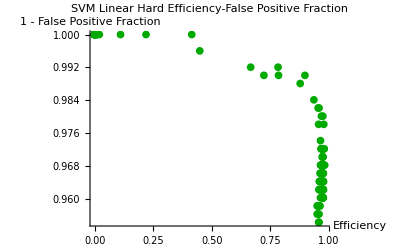

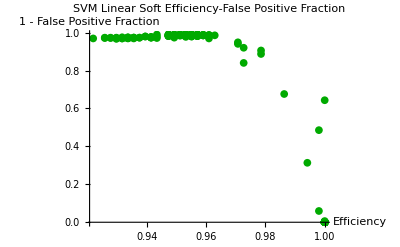

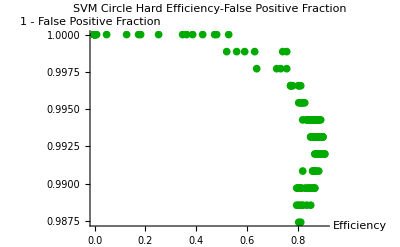

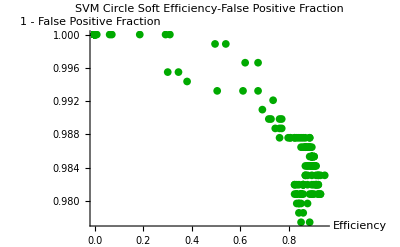

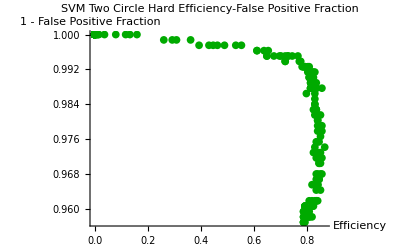

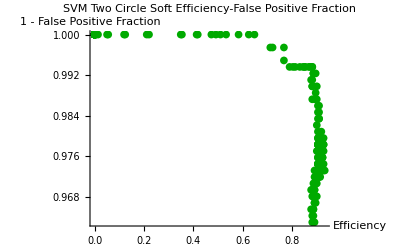

```mathematica
SVMLinearHardEFPPlot
SVMLinearSoftEFPPlot

SVMCircleHardEFPPlot
SVMCircleSoftEFPPlot

SVMTwoCircleHardEFPPlot
SVMTwoCircleSoftEFPPlot
```

#### Efficiency-(1 - False Negative Fraction)

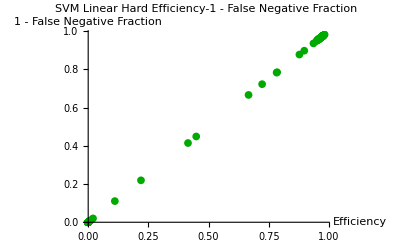

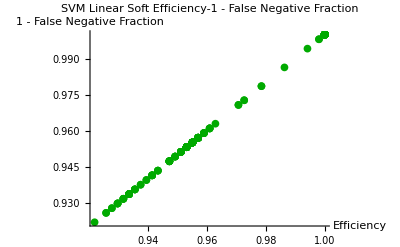

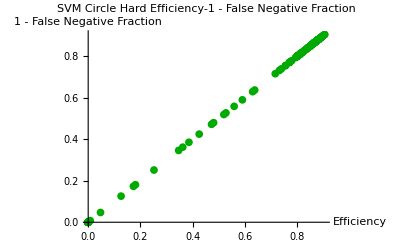

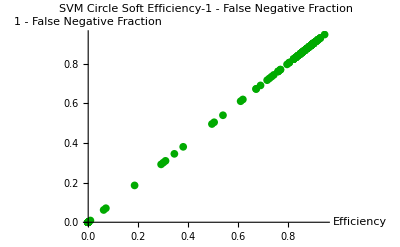

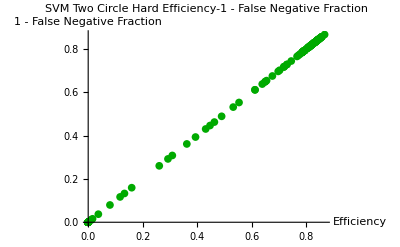

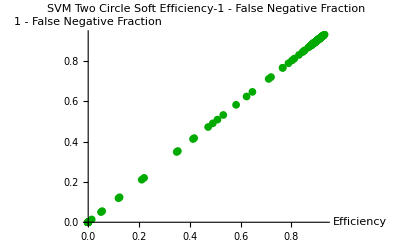

```mathematica
SVMLinearHardEFNPlot
SVMLinearSoftEFNPlot

SVMCircleHardEFNPlot
SVMCircleSoftEFNPlot

SVMTwoCircleHardEFNPlot
SVMTwoCircleSoftEFNPlot
```

#### False Positive Fraction-(1-False Negative Fraction)

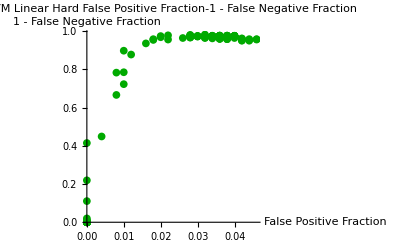

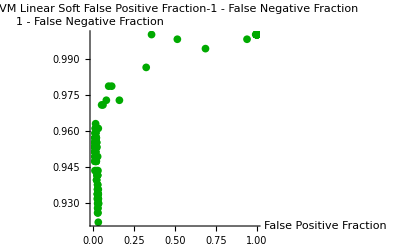

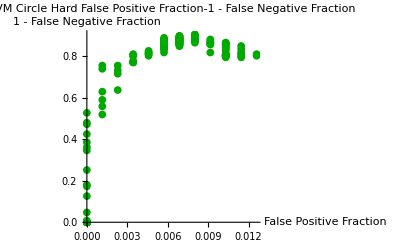

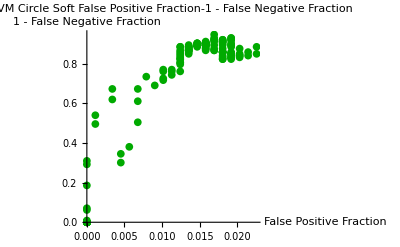

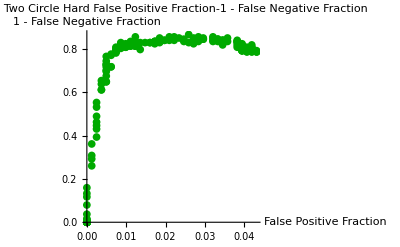

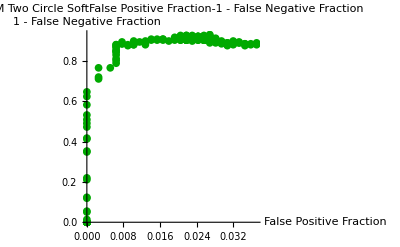

```mathematica
SVMLinearHardFPFNPlot
SVMLinearSoftFPFNPlot

SVMCircleHardFPFNPlot
SVMCircleSoftFPFNPlot

SVMTwoCircleHardFPFNPlot
SVMTwoCircleSoftFPFNPlot
```

### BDS

#### Stumps-Efficiency

```mathematica
BDSLinearHardSEPlot
BDSLinearSoftSEPlot

BDSCircleHardSEPlot
BDSCircleSoftSEPlot

BDSTwoCircleHardSEPlot
BDSTwoCircleSoftSEPlot
```

#### Efficiency-1 - False Positive Fraction

```mathematica
BDSLinearHardEFPPlot
BDSLinearSoftEFPPlot

BDSCircleHardEFPPlot
BDSCircleSoftEFPPlot

BDSTwoCircleHardEFPPlot
BDSTwoCircleSoftEFPPlot
```

#### Efficiency-1 - False Negative Fraction

```mathematica
BDSLinearHardEFNPlot
BDSLinearSoftEFNPlot

BDSCircleHardEFNPlot
BDSCircleSoftEFNPlot

BDSTwoCircleHardEFNPlot
BDSTwoCircleSoftEFNPlot
```

#### False Positive Fraction-1 - False Negative Fraction

```mathematica
BDSLinearHardFPFNPlot
BDSLinearSoftFPFNPlot

BDSCircleHardFPFNPlot
BDSCircleSoftFPFNPlot

BDSTwoCircleHardFPFNPlot
BDSTwoCircleSoftFPFNPlot
```

### BDT

#### Trees-Efficiency

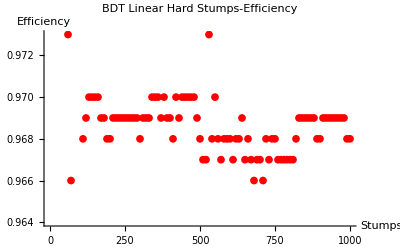

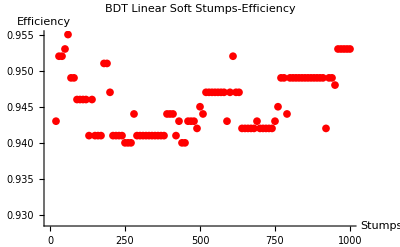

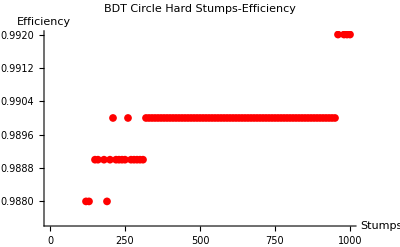

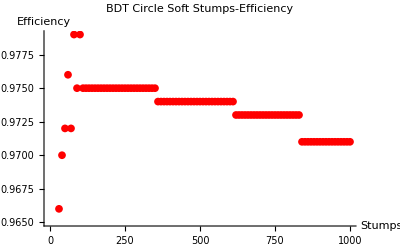

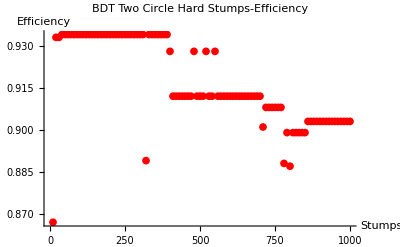

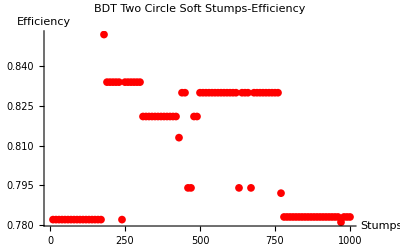

```mathematica
BDTLinearHardTEPlot
BDTLinearSoftTEPlot

BDTCircleHardTEPlot
BDTCircleSoftTEPlot

BDTTwoCircleHardTEPlot
BDTTwoCircleSoftTEPlot
```

#### Efficiency-1 - False Positive Fraction

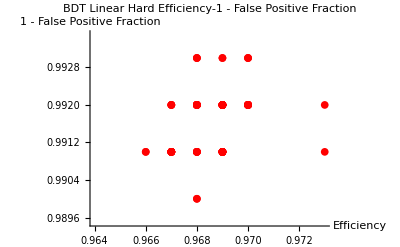

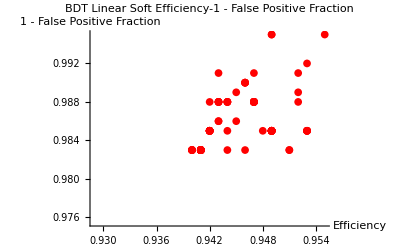

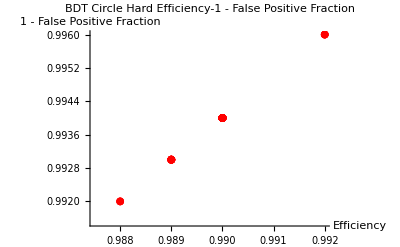

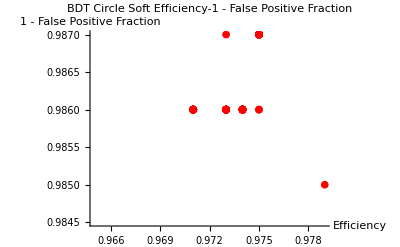

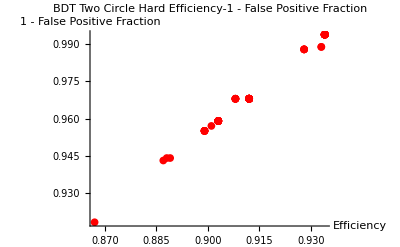

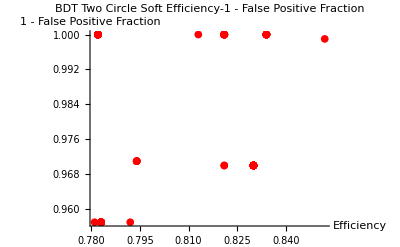

```mathematica
BDTLinearHardEFPPlot
BDTLinearSoftEFPPlot

BDTCircleHardEFPPlot
BDTCircleSoftEFPPlot

BDTTwoCircleHardEFPPlot
BDTTwoCircleSoftEFPPlot
```

#### Efficiency-1 - False Negative Fraction

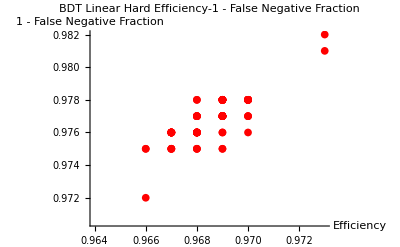

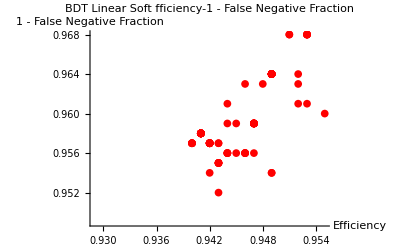

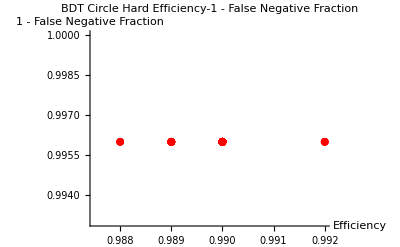

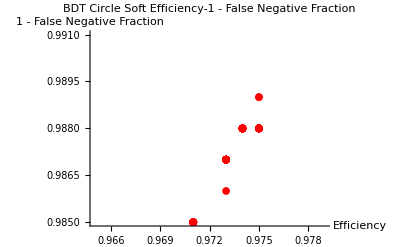

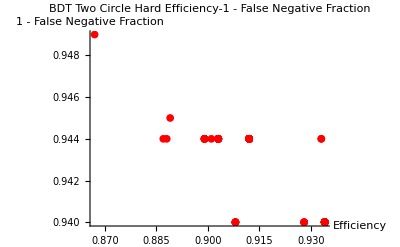

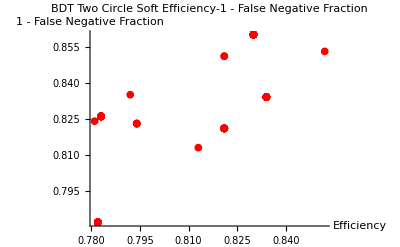

```mathematica
BDTLinearHardEFNPlot
BDTLinearSoftEFNPlot

BDTCircleHardEFNPlot
BDTCircleSoftEFNPlot

BDTTwoCircleHardEFNPlot
BDTTwoCircleSoftEFNPlot
```

#### False Positive Fraction-1 - False Negative Fraction

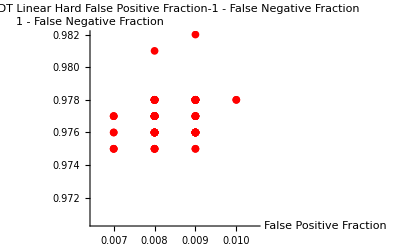

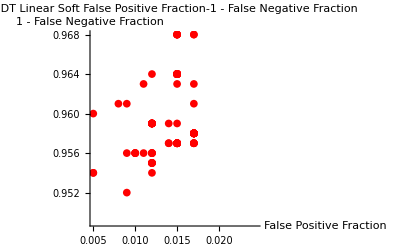

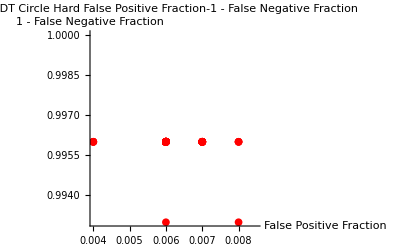

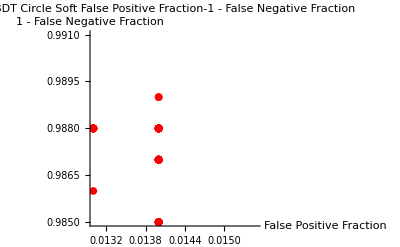

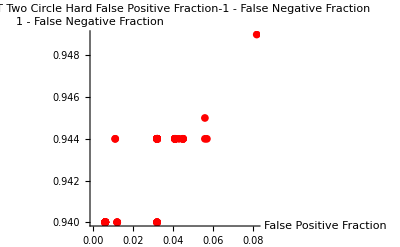

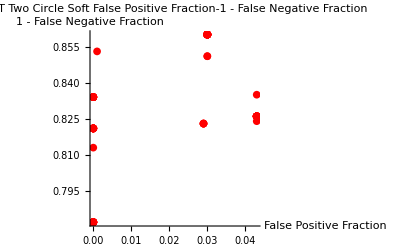

```mathematica
BDTLinearHardFPFNPlot
BDTLinearSoftFPFNPlot

BDTCircleHardFPFNPlot
BDTCircleSoftFPFNPlot

BDTTwoCircleHardFPFNPlot
BDTTwoCircleSoftFPFNPlot
```

### Merged

#### False Positive Fraction- 1 - False Negative Fraction

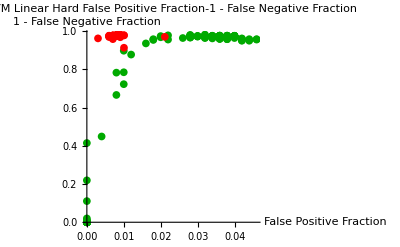

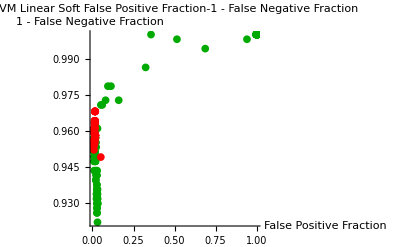

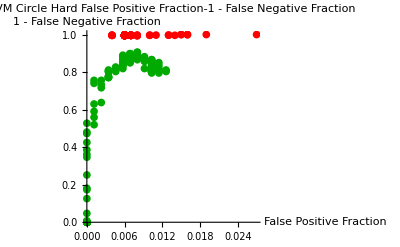

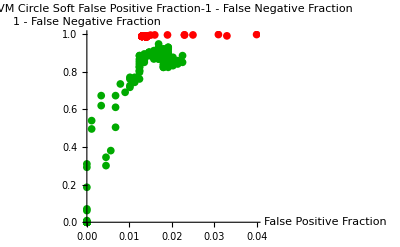

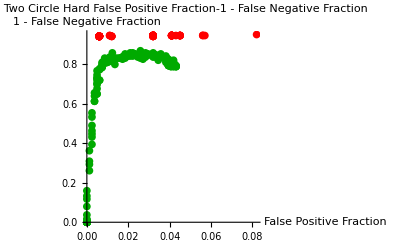

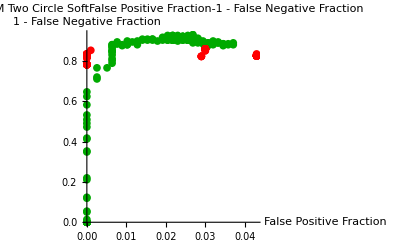

```mathematica
Show[SVMLinearHardFPFNPlot,BDSLinearHardFPFNPlot,BDTLinearHardFPFNPlot,PlotRange-> All]
Show[SVMLinearSoftFPFNPlot,BDSLinearSoftFPFNPlot,BDTLinearSoftFPFNPlot,PlotRange-> All]

Show[SVMCircleHardFPFNPlot,BDSCircleHardFPFNPlot,BDTCircleHardFPFNPlot,PlotRange-> All]
Show[SVMCircleSoftFPFNPlot,BDSCircleSoftFPFNPlot,BDTCircleSoftFPFNPlot,PlotRange-> All]

Show[SVMTwoCircleHardFPFNPlot,BDSTwoCircleHardFPFNPlot,BDTTwoCircleHardFPFNPlot,PlotRange-> All]
Show[SVMTwoCircleSoftFPFNPlot,BDSTwoCircleSoftFPFNPlot,BDTTwoCircleSoftFPFNPlot,PlotRange-> All]
```